```mathematica
Morig = {{0,I*J,I*ϵ,-I*J,0,0,-I*ϵ,0,0},{I*J,I*β-Γ,I*ϵ,0,-I*J,0,0,-I*ϵ,0},{I*ϵ,I*ϵ,I*θ-Γ,0,0,-I*J,0,0,-I*ϵ},{-I*J,0,0,-I*β-Γ,I*J,I*ϵ,-I*ϵ,0,0},{0,-I*J,0,I*J,0,I*ϵ,0,-I*ϵ,0},{0,0,-I*J,I*ϵ,I*ϵ,I*τ-Γ,0,0,-I*ϵ},{-I*ϵ,0,0,-I*ϵ,0,0,-I*θ-Γ,I*J,I*ϵ},{0,-I*ϵ,0,0,-I*ϵ,0,I*J,-I*τ-Γ,I*ϵ},{0,0,-I*ϵ,0,0,-I*ϵ,I*ϵ,I*ϵ,0}};
Morig //TableForm
```

0 | ⅈ J | ⅈ ϵ | -ⅈ J | 0 | 0 | -ⅈ ϵ | 0 | 0
ⅈ J | ⅈ β-Γ | ⅈ ϵ | 0 | -ⅈ J | 0 | 0 | -ⅈ ϵ | 0
ⅈ ϵ | ⅈ ϵ | -Γ+ⅈ θ | 0 | 0 | -ⅈ J | 0 | 0 | -ⅈ ϵ
-ⅈ J | 0 | 0 | -ⅈ β-Γ | ⅈ J | ⅈ ϵ | -ⅈ ϵ | 0 | 0
0 | -ⅈ J | 0 | ⅈ J | 0 | ⅈ ϵ | 0 | -ⅈ ϵ | 0
0 | 0 | -ⅈ J | ⅈ ϵ | ⅈ ϵ | -Γ+ⅈ τ | 0 | 0 | -ⅈ ϵ
-ⅈ ϵ | 0 | 0 | -ⅈ ϵ | 0 | 0 | -Γ-ⅈ θ | ⅈ J | ⅈ ϵ
0 | -ⅈ ϵ | 0 | 0 | -ⅈ ϵ | 0 | ⅈ J | -Γ-ⅈ τ | ⅈ ϵ
0 | 0 | -ⅈ ϵ | 0 | 0 | -ⅈ ϵ | ⅈ ϵ | ⅈ ϵ | 0

```mathematica
M = Morig /. {Γ->10^(-5), J->0.1, β->0, θ->10^(-4), τ->10^(-4)}
```

{{0,0.+0.1 ⅈ,ⅈ ϵ,0.-0.1 ⅈ,0,0,-ⅈ ϵ,0,0},{0.+0.1 ⅈ,-1/100000,ⅈ ϵ,0,0.-0.1 ⅈ,0,0,-ⅈ ϵ,0},{ⅈ ϵ,ⅈ ϵ,-1/100000+ⅈ/10000,0,0,0.-0.1 ⅈ,0,0,-ⅈ ϵ},{0.-0.1 ⅈ,0,0,-1/100000,0.+0.1 ⅈ,ⅈ ϵ,-ⅈ ϵ,0,0},{0,0.-0.1 ⅈ,0,0.+0.1 ⅈ,0,ⅈ ϵ,0,-ⅈ ϵ,0},{0,0,0.-0.1 ⅈ,ⅈ ϵ,ⅈ ϵ,-1/100000+ⅈ/10000,0,0,-ⅈ ϵ},{-ⅈ ϵ,0,0,-ⅈ ϵ,0,0,-1/100000-ⅈ/10000,0.+0.1 ⅈ,ⅈ ϵ},{0,-ⅈ ϵ,0,0,-ⅈ ϵ,0,0.+0.1 ⅈ,-1/100000-ⅈ/10000,ⅈ ϵ},{0,0,-ⅈ ϵ,0,0,-ⅈ ϵ,ⅈ ϵ,ⅈ ϵ,0}}

```mathematica
(* =========================================*)(*Parameters*)(* =========================================*)
epsilonStart = 10^(-6);
epsilonStop=0.099999;
step=10^(-5);

outfile=FileNameJoin[{NotebookDirectory[],"gamma=1e-5; J=0.1; delta_32=delta_31=1e-4; delta_21=0.dat"}];


(* =========================================*)
(*Generate epsilon values*)
(* =========================================*)

epsList=Range[epsilonStart,epsilonStop,step];

(*Number of eigenvalues*)
nEvals=Length[Eigenvalues[M/. ϵ->First[epsList]]];

(* =========================================*)
(*Build data table*)
(* =========================================*)

data=Table[Module[{ev},ev=Sort[N[Eigenvalues[N[M /. ϵ -> eps]]]];
Join[{N[eps]},Flatten[{Re[#], Im[#]}&/@ev]]],{eps,epsList}];


(* =========================================*)
(*Export*)
(* =========================================*)

Export[outfile,data,"Table"];

Print["Saved ",Length[data]," rows to ",outfile];
```

Saved 10000 rows to /cptg/u4/kratzel/Documents/Wolfram Mathematica/[3.1] [three-site (non-degenerate), single-body, general epsilons, local dephasing] [june 12]/gamma=1e-5; J=0.1; delta_32=delta_31=1e-4; delta_21=0.dat

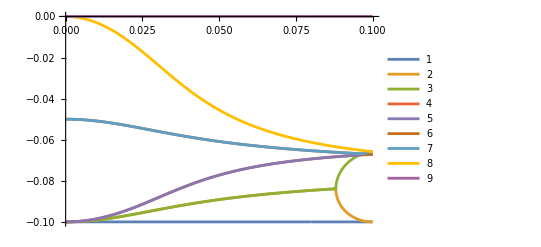

```mathematica
ListLinePlot[data[[All,{1,#}]]&/@Range[2,Length[data[[1]]],2],PlotLegends->Automatic]
```